# MFEM Mesh Generation

Instructions:
Use mesh tools to create an ElementMesh object for the mesh that you want. 
Set the proper conditions for the BoundaryElement attributes.
For 2D write “2” after numVertices.
Set the proper numbers for element type and boundary element type. 
Set the proper dimension.
Add all the relevant boundaryElement lists.
Export.

```mathematica
<<NDSolve`FEM`
<<MeshTools`
(*<<Notation`*)
<< HKLaTeXWrite`
```

## 2D meshes

## Small Square. Quads

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<<Notation`
<< HKLaTeXWrite`
```

```mathematica
a = 0.1;
```

ElementMesh[{{0.,0.1},{0.,0.1}},{QuadElement[<1600>]}]

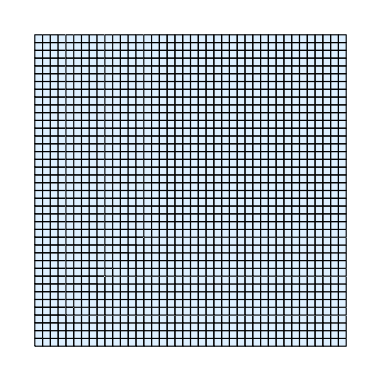

```mathematica
mesh =RectangleMesh[{0,0},{a,a},{40,40}]
Show[mesh["Wireframe"["MeshElementStyle"->FaceForm[LightBlue]]]]
```

```mathematica
coords=mesh["Coordinates"]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

1600

### Boundary Element sections

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

160

```mathematica
boundaryElements[[1;;15]]
```

{{1,42},{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},{8,7},{9,8},{10,9},{11,10},{12,11},{13,12},{14,13},{15,14}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
(* boundary at Y=0 *)
boundaryElements1 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Y=1 *)
boundaryElements2 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]] >= (a-0.0001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at X=0 *)
boundaryElements3 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] <= 0.0001, count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at x=a *)
boundaryElements4 := Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] >= (a-0.0001), count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
]
```

```mathematica
boundaryElements//Length
Total@(Length/@{boundaryElements1,boundaryElements2,boundaryElements3,boundaryElements4})
```

160

160

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[2],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 3 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 1 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 1 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 1 ",(*3=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
boundarySection4=StringJoin[
StringJoin[Table[StringJoin["4 1 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements4}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"2"<>"\n\n",elementSection1,"\n",boundarySection1,boundarySection2,boundarySection3,boundarySection4,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/Square12cm-quad.mesh",mfemMeshContent,"Text"]
```

../input/meshes/Square12cm-quad.mesh

## Square with side slit. Unstructured mesh. Triangles

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<< HKLaTeXWrite`
```

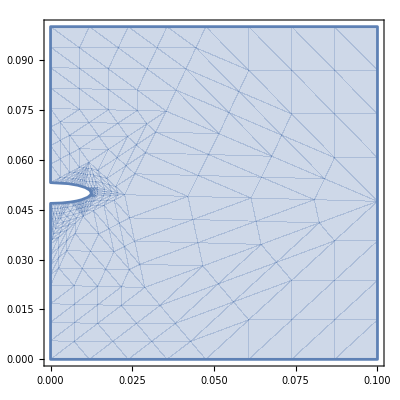

```mathematica
a=0.1;
region=ImplicitRegion[(0<=x<=a)&&(0<=y<=a)&&((x)^2+(y-0.05)^2/0.25^2>=0.0125^2),{x,y}];
RegionPlot[region]
```

ElementMesh[{{0.,0.1},{0.,0.1}},{TriangleElement[<3378>]}]

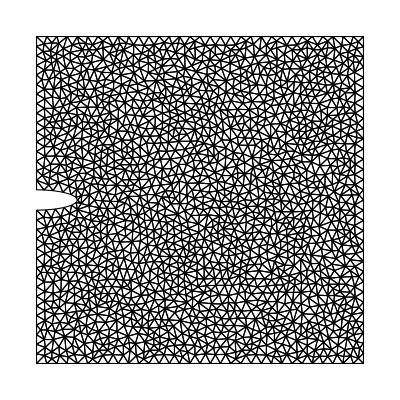

```mathematica
mesh=ToElementMesh[region,MaxCellMeasure->{"Volume"->10^-8},"MeshElementType"->"TriangleElement","MeshOrder"->1]
mesh["Wireframe"]
```

```mathematica
coords=mesh["Coordinates"]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

3378

### Boundary Element sections

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

140

```mathematica
boundaryElements[[1;;15]]
```

{{68,1},{69,68},{70,69},{71,70},{72,71},{73,72},{74,73},{75,74},{76,75},{77,76},{78,77},{79,78},{80,79},{81,80},{82,81}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
(* boundary at Y=0 *)
boundaryElements1 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Y=1 *)
boundaryElements2 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]] >= (a-0.0001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(*(* boundary at X=0 *)
boundaryElements3 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] <= 0.0001, count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];*)
```

```mathematica
(* boundary at x=a *)
boundaryElements4 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] >= (a-0.0001), count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
boundaryElements3=UniqueElements[{boundaryElements,Join[boundaryElements1,boundaryElements2,boundaryElements4]}][[1]];
```

```mathematica
boundaryElements//Length
Total@(Length/@{boundaryElements1,boundaryElements2,boundaryElements3,boundaryElements4})
```

140

140

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[2],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 2 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 1 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 1 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 1 ",(*3=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
boundarySection4=StringJoin[
StringJoin[Table[StringJoin["4 1 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements4}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"2"<>"\n\n",elementSection1,"\n",boundarySection1,boundarySection2,boundarySection3,boundarySection4,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/SquareWithSlit-tri.mesh",mfemMeshContent,"Text"]
```

../input/meshes/SquareWithSlit-tri.mesh

## Square. Unstructured mesh. Triangles

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<< HKLaTeXWrite`
```

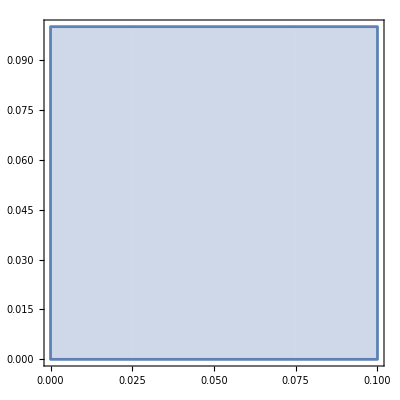

```mathematica
a=0.1;
region=Rectangle[{0,0},{a,a}];
RegionPlot[region]
```

ElementMesh[{{0.,0.1},{0.,0.1}},{TriangleElement[<3452>]}]

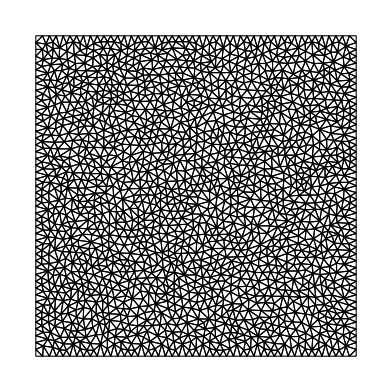

```mathematica
mesh=ToElementMesh[region,MaxCellMeasure->{"Volume"->10^-8},"MeshElementType"->"TriangleElement","MeshOrder"->1]
(*mesh=RectangleMesh[{0,0},{a,a},{1,1}]*)
mesh["Wireframe"]
```

```mathematica
coords=mesh["Coordinates"]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

3452

### Boundary Element sections

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

188

```mathematica
boundaryElements[[1;;4]]
```

{{49,1},{1,2},{2,3},{3,4}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
(* boundary at Y=0 *)
boundaryElements1 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Y=1 *)
boundaryElements2 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]] >= (a-0.0001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at X=0 *)
boundaryElements3 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] <= 0.0001, count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at x=a *)
boundaryElements4 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] >= (a-0.0001), count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
boundaryElements//Length
(Length/@{boundaryElements1,boundaryElements2,boundaryElements3,boundaryElements4})
```

188

{47,47,47,47}

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[2],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 2 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 1 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 1 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 1 ",(*3=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
boundarySection4=StringJoin[
StringJoin[Table[StringJoin["4 1 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements4}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"2"<>"\n\n",elementSection1,"\n",boundarySection1,boundarySection2,boundarySection3,boundarySection4,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/Square-tri.mesh",mfemMeshContent,"Text"]
```

../input/meshes/Square-tri.mesh

## Beam. Unstructured mesh. Triangles

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<< HKLaTeXWrite`
```

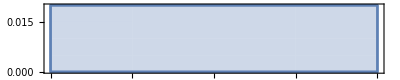

```mathematica
a=0.1;
b=0.02;
region=Rectangle[{0,0},{a,b}];
RegionPlot[region,AspectRatio->b/a]
```

ElementMesh[{{0.,0.1},{0.,0.02}},{QuadElement[<500>]}]

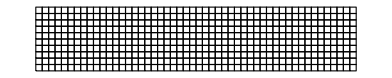

```mathematica
(*mesh=ToElementMesh[region,MaxCellMeasure->{"Volume"->10^-8},"MeshElementType"->"TriangleElement","MeshOrder"->1]*)
mesh=RectangleMesh[{0,0},{a,b},{50,10}]
mesh["Wireframe"]
```

```mathematica
coords=mesh["Coordinates"]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

500

### Boundary Element sections

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

120

```mathematica
boundaryElements[[1;;4]]
```

{{1,12},{2,1},{3,2},{4,3}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
(* boundary at Y=0 *)
boundaryElements1 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Y=1 *)
boundaryElements2 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]] >= (b-0.0001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at X=0 *)
boundaryElements3 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] <= 0.0001, count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at x=a *)
boundaryElements4 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] >= (a-0.0001), count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
boundaryElements//Length
(Length/@{boundaryElements1,boundaryElements2,boundaryElements3,boundaryElements4})
```

120

{50,50,10,10}

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[2],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 3 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 1 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 1 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 1 ",(*3=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
boundarySection4=StringJoin[
StringJoin[Table[StringJoin["4 1 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements4}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"2"<>"\n\n",elementSection1,"\n",boundarySection1,boundarySection2,boundarySection3,boundarySection4,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/Beam-quad.mesh",mfemMeshContent,"Text"]
```

../input/meshes/Beam-quad.mesh

## Circle, no attributes. Unstructured mesh. Triangles

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<< HKLaTeXWrite`
```

```mathematica
radius=0.025;
region=Disk[{0,0},radius];
```

```mathematica
elArea=9*10^-6;
meshrefFunc=Function[{vertices,Area},
Block[{x,y,tol},
{x,y}=Mean[vertices];
tol=0.001;
If[ Sqrt[x^2+y^2]>radius-tol ,Area<elArea,Area>elArea]
]];
```

ElementMesh[{{-0.025,0.025},{-0.025,0.025}},{TriangleElement[<3048>]}]

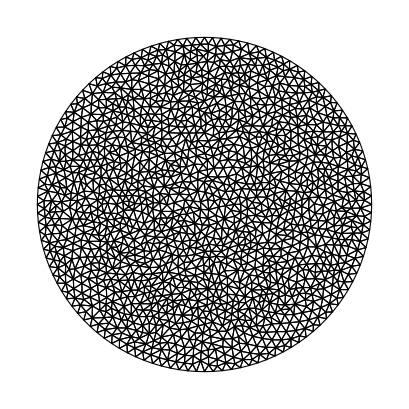

```mathematica
mesh=ToElementMesh[region,MaxCellMeasure->{"Area"->10^-6},"MeshElementType"->"TriangleElement","MeshOrder"->1(*,MeshRefinementFunction->meshrefFunc*)]
mesh["Wireframe"]
```

```mathematica
coords=mesh["Coordinates"];
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

3048

### Boundary Element sections

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

116

```mathematica
boundaryElements[[1;;15]]
```

{{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},{8,7},{9,8},{10,9},{11,10},{12,11},{13,12},{14,13},{15,14},{16,15}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
(*
boundaryElements1 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];*)
```

```mathematica
(*boundaryElements3=UniqueElements[{boundaryElements,Join[boundaryElements1,boundaryElements2]}][[1]];*)
```

```mathematica
boundaryElements//Length
```

116

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[2],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],10]]," ",ToString[NumberForm[x[[2]],10]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 2 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 1 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements}]]];
```

```mathematica
(*boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 1 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];*)
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"2"<>"\n\n",elementSection1,"\n",boundarySection1,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/circle_BacteriaSwarm-tri.mesh",mfemMeshContent,"Text"]
```

../input/meshes/circle_BacteriaSwarm-tri.mesh

## Annulus, no attributes. Unstructured mesh. Triangles

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<< HKLaTeXWrite`
```

```mathematica
{rin,rout}={0.0175,0.025};
region=Annulus[{0,0},{rin,rout}];
```

```mathematica
elArea=9*10^-6;
meshrefFunc=Function[{vertices,Area},
Block[{x,y,tol},
{x,y}=Mean[vertices];
tol=0.001;
If[ Sqrt[x^2+y^2]>radius-tol ,Area<elArea,Area>elArea]
]];
```

ElementMesh[{{-0.025,0.025},{-0.0249945,0.0249945}},{TriangleElement[<3000>]}]

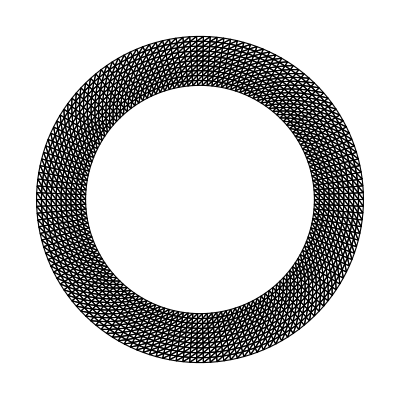

```mathematica
annulusmesh=AnnulusMesh[{0,0},{rin,rout},{150,10}];
mesh=QuadToTriangleMesh[annulusmesh]
mesh["Wireframe"]
```

```mathematica
(*mesh=ToElementMesh[region,MaxCellMeasure->{"Area"->2.5*10^-7},"MeshElementType"->"TriangleElement","MeshOrder"->1(*,MeshRefinementFunction->meshrefFunc*)]
mesh["Wireframe"]*)
```

```mathematica
coords=Chop[#,10^-8]&/@mesh["Coordinates"];
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

3000

### Boundary Element sections

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

300

```mathematica
boundaryElements[[1;;15]]
```

{{1,12},{22,11},{12,23},{33,22},{23,34},{44,33},{34,45},{55,44},{45,56},{66,55},{56,67},{77,66},{67,78},{88,77},{78,89}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
boundaryElements1 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
(elcoords[[n,1]]^2+elcoords[[n,2]]^2)<= (rin+10^-8)^2 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
boundaryElements2 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
(elcoords[[n,1]]^2+elcoords[[n,2]]^2)>= (rout-10^-8)^2 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
boundaryElements//Length
Total@(Length/@{boundaryElements1,boundaryElements2})
```

300

300

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[2],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],10]]," ",ToString[NumberForm[x[[2]],10]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 2 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 1 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 1 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"2"<>"\n\n",elementSection1,"\n",boundarySection1,boundarySection2,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/annulus2_bdrattr-tri.mesh",mfemMeshContent,"Text"]
```

../input/meshes/annulus2_bdrattr-tri.mesh

## Long bar with assymetric notch. Unstructured mesh. Quads. (From Abaqus to MFEM)

### Read Mesh

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
mfemMesh=Import["../input/meshes/symmetric_notch.mesh","Table"];
```

```mathematica
GetElements[mfemMesh_]:=Module[{sectionstart=0,rowstart=1,rowend,row,elementSections,elAttrs,elTypes,bdrelementSections,bdrelAttrs,bdrelTypes,vertices,coords,numOfElAttrs,numOfBdrAttrs,dimension},

Do[
If[mfemMesh[[listRow]]=={"dimension"},dimension=mfemMesh[[listRow+1,1]];];
,{listRow,1,Length@mfemMesh}];


{rowstart,rowend}={1,1};

Do[
If[mfemMesh[[listRow]]=={"elements"},rowstart=listRow+2;];

If[rowstart>1&&listRow>rowstart&&Length[mfemMesh[[listRow]]]!=Length[mfemMesh[[rowstart]]],
rowend=listRow-1;Break[];
];
,{listRow,1,Length@mfemMesh}];

elementSections=(mfemMesh[[rowstart;;rowend]])[[;;,3;;]]+1;
elAttrs=(mfemMesh[[rowstart;;rowend]])[[;;,1]];
elTypes=(mfemMesh[[rowstart;;rowend]])[[;;,2]];

{rowstart,rowend}={1,1};

Do[
If[mfemMesh[[listRow]]=={"boundary"},rowstart=listRow+2;];

If[rowstart>1&&listRow>rowstart&&Length[mfemMesh[[listRow]]]!=Length[mfemMesh[[rowstart]]],
rowend=listRow-1;Break[];
];
,{listRow,1,Length@mfemMesh}];

bdrelementSections=(mfemMesh[[rowstart;;rowend]])[[;;,3;;]]+1;
bdrelAttrs=(mfemMesh[[rowstart;;rowend]])[[;;,1]];
bdrelTypes=(mfemMesh[[rowstart;;rowend]])[[;;,2]];

{rowstart,rowend}={1,1};

Do[
If[mfemMesh[[listRow]]=={"vertices"},sectionstart=listRow;];
	

If[sectionstart!=0&&rowstart==1&&listRow>sectionstart+2&&(Head[mfemMesh[[listRow,1]]]==Integer||Head[mfemMesh[[listRow,1]]]==Real),rowstart=listRow;];

If[rowstart>1&&listRow>rowstart&&Length[mfemMesh[[listRow]]]!=Length[mfemMesh[[rowstart]]],
rowend=listRow;Break[];
];
If[rowstart>1&&listRow>rowstart&&listRow==Length@mfemMesh,
rowend=listRow;Break[];
];

,{listRow,1,Length@mfemMesh}];

coords=mfemMesh[[rowstart;;rowend]];

vertices=Table[Table[coords[[i+((n-1)*dimension)]],{i,1,dimension}],{n,1,Length[coords]/dimension}];

{{elementSections,elAttrs,elTypes},{bdrelementSections,bdrelAttrs,bdrelTypes},{vertices,coords}}
(*{sectionstart,rowstart,rowend}*)
]
```

```mathematica
{{elements,elAttrs,elTypes},{boundaryElements,bdrelAttrs,bdrelTypes},{vertices,coords}}=GetElements[mfemMesh];
```

```mathematica
{elements//Max,coords//Length}
```

{33275,33275}

```mathematica
coords[[1;;5]]
elements[[1;;2]]
```

{{0.250117,0.1},{0.250117,-0.00056},{2.5,0},{2.5,0.4},{0.250117,0.4}}

{{378,13262,1012,13},{376,13276,13263,377}}

### Make mesh

```mathematica
mesh=ToElementMesh["Coordinates"->coords,"MeshElements"-> {QuadElement[elements]},"BoundaryElements"->{LineElement[boundaryElements]},"MeshOrder"->1]
```

ElementMesh[{{-2.5,2.5},{-0.00067,0.55}},{QuadElement[<33154>]}]

```mathematica
{numVertices,numElements,numBoundary}=Length/@{coords,elements,boundaryElements}
```

{33275,33154,240}

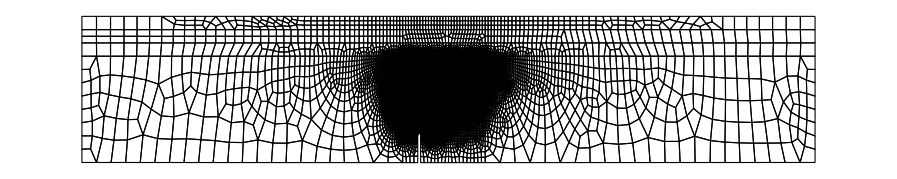

```mathematica
mesh["Wireframe"]
```

```mathematica
DeleteDuplicates[Flatten[elements]]//Length
```

33275

### Boundary Element sections

```mathematica
boundaryElements[[1;;4]]
```

{{12,9},{1356,32},{30,1356},{4,12}}

```mathematica
(* Assign boundary attributes *)
```

Boundary attributes:
1 - Leftmost bottom element
2 - Rightmost bottom element
3 - 2 elements centered around (0.000117,0.550000)
4 - Rest of the boundary

1, 2, 3 are essential boundaries

Left and right most coords

```mathematica
{a,b}={Min@coords[[;;,1]],Max@coords[[;;,1]]}
base=Min@coords[[;;,2]]
pointc={0.000117,0.550000}
```

{-2.5,2.5}

```mathematica
(* boundary element at (-2.5, 0)  *)
boundaryElements1 = Module[{elcoords,belements,zcoords,count,point},
belements = {};
point={a,base};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
Abs[elcoords[[n,1]]-point[[1]]]<=0.1 &&Abs[elcoords[[n,2]]-point[[2]]]<=0.005, count+=1;
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i];Echo[elcoords];
 ];
,{i,boundaryElements}];
belements
];
```

{{-2.5,0},{-2.40056,-0.000029}}

```mathematica
(* boundary at (2.5, 0) *)
boundaryElements2 = Module[{elcoords,belements,zcoords,count,point},
belements = {};
point={b,base};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
Abs[elcoords[[n,1]]-point[[1]]]<=0.2 &&Abs[elcoords[[n,2]]-point[[2]]]<=0.005, count+=1;
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i];Echo[elcoords];
 ];
,{i,boundaryElements}];
belements
];
```

{{2.39773,-0.000025},{2.5,0}}

```mathematica
boundaryElements2
```

{{57,3}}

```mathematica
(* boundary around (0.000117, 0.550000) *)
boundaryElements3 = Module[{elcoords,belements,zcoords,count,point},
belements={};
point={0.000117, 0.550000};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
Abs[elcoords[[n,1]]-point[[1]]]<=0.02 &&Abs[elcoords[[n,2]]-point[[2]]]<=0.005, count+=1;
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i];Echo[elcoords];
 ];
,{i,boundaryElements}];
belements
];
```

{{0.019348,0.55},{0.000117,0.55}}

{{0.000117,0.55},{-0.019414,0.55}}

```mathematica
boundaryElements3
```

{{997,24},{24,1309}}

```mathematica
(*boundaryElements4*)
boundaryElements4=UniqueElements[{boundaryElements,Join[boundaryElements1,boundaryElements2,boundaryElements3]}][[1]];
```

```mathematica
boundaryElements//Length
(Length/@{boundaryElements1,boundaryElements2,boundaryElements3,boundaryElements4})
```

240

{1,1,2,236}

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[2],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 3 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 1 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 1 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 1 ",(*3=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
boundarySection4=StringJoin[
StringJoin[Table[StringJoin["4 1 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements4}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"2"<>"\n\n",elementSection1,"\n",boundarySection1,boundarySection2,boundarySection3,boundarySection4,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/symmetric_notch_bdrattr-quad.mesh",mfemMeshContent,"Text"]
```

../input/meshes/symmetric_notch_bdrattr-quad.mesh

## 3D meshes

## Plate with side slit. Unstructured mesh. Tets

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<< HKLaTeXWrite`
```

```mathematica
a=0.1;
t=0.005;
region=ImplicitRegion[(0<=x<=a)&&(0<=y<=a)&&(0<=z<=t)&&((x)^2+(y-0.05)^2/0.125^2+(z-0.0025)^2>=0.0125^2),{x,y,z}];
Show[DiscretizeRegion[region],ViewPoint->Above]
```

-Graphics3D-

```mathematica
mesh=ToElementMesh[region,MaxCellMeasure->{"Volume"->10^-8},"MeshElementType"->"TetrahedronElement","MeshOrder"->1]
Show[mesh["Wireframe"],ViewPoint->Above]
```

ElementMesh[{{0.,0.1},{0.,0.1},{0.,0.005}},{TetrahedronElement[<27414>]}]

-Graphics3D-

```mathematica
coords=mesh["Coordinates"]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

27414

### Boundary Element sections

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

15028

```mathematica
boundaryElements[[1;;15]]
```

{{4660,4474,4470},{4658,4660,4470},{4476,4661,4472},{4661,4659,4472},{4662,4478,4474},{4662,4474,4660},{4480,4663,4476},{4663,4661,4476},{4664,4482,4478},{4664,4478,4662},{4484,4665,4480},{4665,4663,4480},{4666,4486,4482},{4666,4482,4664},{4488,4667,4484}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
(* boundary at Y=0 *)
boundaryElements1 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Y=a *)
boundaryElements2 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]] >= (a-0.0001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(*(* boundary at X=0 *)
boundaryElements3 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] <= 0.0001, count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];*)
```

```mathematica
(*(* boundary at x=a *)
boundaryElements4 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] >= (a-0.0001), count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];*)
```

```mathematica
boundaryElements3=UniqueElements[{boundaryElements,Join[boundaryElements1,boundaryElements2]}][[1]];
```

```mathematica
boundaryElements//Length
(Length/@{boundaryElements1,boundaryElements2,boundaryElements3})
```

15028

{911,931,13186}

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[3],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]]," ",ToString[NumberForm[x[[3]],7]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 4 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 2 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 2 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 2 ",(*3=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
(*boundarySection4=StringJoin[
StringJoin[Table[StringJoin["4 1 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements4}]]];*)
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"3"<>"\n\n",elementSection1,"\n",boundarySection1,boundarySection2,boundarySection3,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/ThinPlateWithSlit-tet.mesh",mfemMeshContent,"Text"]
```

../input/meshes/ThinPlateWithSlit-tet.mesh

## Slab with bottom notch. Unstructured mesh. Tets

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<< HKLaTeXWrite`
```

```mathematica
a=0.1;
b=0.04;
t=0.005;
trianglebase=0.0025;
triangleheight=0.0075;
region1 = Rectangle[{0,0},{a,b}];
region2 = Triangle[{{a/2,0+triangleheight},{a/2-trianglebase/2,0},{a/2+trianglebase/2,0}}];
region3=RegionDifference[region1,region2];
region4=RegionProduct[region3,Line[{{0},{t}}]];
Region[region4];
```

```mathematica
mesh=ToElementMesh[region4,MaxCellMeasure->{"Volume"->10^-8},"MeshElementType"->"TetrahedronElement","MeshOrder"->1]
Show[mesh["Wireframe"],ViewPoint->{0, 0, 1}]
```

ElementMesh[{{0.,0.1},{0.,0.04},{0.,0.005}},{TetrahedronElement[<4100>]}]

-Graphics3D-

```mathematica
coords=mesh["Coordinates"]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

4100

### Boundary Element sections

Boundary elements sections are as follows:
1. Normal vec: (-1,0,0)
2. Normal vec: (1,0,0)
3. Normal vec: (0,-1,0)
4. Normal vec: (0,1,0)
5. Normal vec: (0,0-1)
6. Normal vec: (0,0,1)
7. Notch elements

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

2244

```mathematica
boundaryElements[[1;;15]]
```

{{41,781,481},{241,457,21},{769,1005,471},{375,928,97},{234,45,438},{386,652,205},{692,944,222},{213,1114,14},{821,831,822},{182,359,357},{294,295,3},{616,1102,351},{296,1076,550},{407,1115,121},{619,1102,354}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
(* boundary at X=0 *)
boundaryElements1 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at X=a *)
boundaryElements2=Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]]>= (a-0.00001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Y=0 *)
boundaryElements3=Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Y=b *)
boundaryElements4=Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]>= (b-0.00001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Z=0 *)
boundaryElements5=Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Z=t *)
boundaryElements6=Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]>= (t-0.00001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
boundaryElements7=UniqueElements[{boundaryElements,Join[boundaryElements1,boundaryElements2,boundaryElements3,boundaryElements4,boundaryElements5,boundaryElements6]}][[1]];
```

```mathematica
boundaryElements//Length
Total@(Length/@{boundaryElements1,boundaryElements2,boundaryElements3,boundaryElements4,boundaryElements5,boundaryElements6,boundaryElements7})
```

2244

2244

```mathematica
ListPointPlot3D[{coords[[DeleteDuplicates@(Flatten@boundaryElements1)]],coords[[DeleteDuplicates@(Flatten@boundaryElements2)]],coords[[DeleteDuplicates@(Flatten@boundaryElements3)]],coords[[DeleteDuplicates@(Flatten@boundaryElements4)]],coords[[DeleteDuplicates@(Flatten@boundaryElements7)]]},ViewPoint->{0,0,1},AspectRatio->b/a]
```

-Graphics3D-

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[3],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],10]]," ",ToString[NumberForm[x[[2]],10]]," ",ToString[NumberForm[x[[3]],10]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 4 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 2 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 2 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 2 ",(*3=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
boundarySection4=StringJoin[
StringJoin[Table[StringJoin["4 2 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements4}]]];
```

```mathematica
boundarySection5=StringJoin[
StringJoin[Table[StringJoin["5 2 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements5}]]];
```

```mathematica
boundarySection6=StringJoin[
StringJoin[Table[StringJoin["6 2 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements6}]]];
```

```mathematica
boundarySection7=StringJoin[
StringJoin[Table[StringJoin["7 2 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements7}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"3"<>"\n\n",elementSection1,"\n",boundarySection1,boundarySection2,boundarySection3,boundarySection4,boundarySection5,boundarySection6,boundarySection7,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/SlabWithNotch2-tet.mesh",mfemMeshContent,"Text"]
```

../input/meshes/SlabWithNotch2-tet.mesh

```mathematica
Ε=20800;
ν=0.3;
λ=(Ε ν)/((1+ν)(1-2ν))
μ=Ε/(2(1+ν))
```

12000.

8000.

## Convert MFEM mesh to MMA mesh

```mathematica
<<NDSolve`FEM`
<<MeshTools`
(*<<Notation`*)
<< HKLaTeXWrite`
```

```mathematica
33154*4
165770
```

132616

165770

```mathematica
2*(vertices//Length)
```

33274

## Read Mesh

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
mfemMesh=Import["../input/meshes/symmetric_notch.mesh","Table"];
```

```mathematica
GetElements[mfemMesh_]:=Module[{sectionstart=0,rowstart=1,rowend,row,elementSections,elAttrs,elTypes,bdrelementSections,bdrelAttrs,bdrelTypes,vertices,coords,numOfElAttrs,numOfBdrAttrs,dimension},

Do[
If[mfemMesh[[listRow]]=={"dimension"},dimension=mfemMesh[[listRow+1,1]];];
,{listRow,1,Length@mfemMesh}];


{rowstart,rowend}={1,1};

Do[
If[mfemMesh[[listRow]]=={"elements"},rowstart=listRow+2;];

If[rowstart>1&&listRow>rowstart&&Length[mfemMesh[[listRow]]]!=Length[mfemMesh[[rowstart]]],
rowend=listRow-1;Break[];
];
,{listRow,1,Length@mfemMesh}];

elementSections=(mfemMesh[[rowstart;;rowend]])[[;;,3;;]]+1;
elAttrs=(mfemMesh[[rowstart;;rowend]])[[;;,1]];
elTypes=(mfemMesh[[rowstart;;rowend]])[[;;,2]];

{rowstart,rowend}={1,1};

Do[
If[mfemMesh[[listRow]]=={"boundary"},rowstart=listRow+2;];

If[rowstart>1&&listRow>rowstart&&Length[mfemMesh[[listRow]]]!=Length[mfemMesh[[rowstart]]],
rowend=listRow-1;Break[];
];
,{listRow,1,Length@mfemMesh}];

bdrelementSections=(mfemMesh[[rowstart;;rowend]])[[;;,3;;]]+1;
bdrelAttrs=(mfemMesh[[rowstart;;rowend]])[[;;,1]];
bdrelTypes=(mfemMesh[[rowstart;;rowend]])[[;;,2]];

{rowstart,rowend}={1,1};

Do[
If[mfemMesh[[listRow]]=={"vertices"},sectionstart=listRow;];
	

If[sectionstart!=0&&rowstart==1&&listRow>sectionstart+2&&(Head[mfemMesh[[listRow,1]]]==Integer||Head[mfemMesh[[listRow,1]]]==Real),rowstart=listRow;];

If[rowstart>1&&listRow>rowstart&&Length[mfemMesh[[listRow]]]!=Length[mfemMesh[[rowstart]]],
rowend=listRow;Break[];
];
If[rowstart>1&&listRow>rowstart&&listRow==Length@mfemMesh,
rowend=listRow;Break[];
];

,{listRow,1,Length@mfemMesh}];

coords=mfemMesh[[rowstart;;rowend]];

vertices=Table[Table[coords[[i+((n-1)*dimension)]],{i,1,dimension}],{n,1,Length[coords]/dimension}];

{{elementSections,elAttrs,elTypes},{bdrelementSections,bdrelAttrs,bdrelTypes},{vertices,coords}}
(*{sectionstart,rowstart,rowend}*)
]
```

```mathematica
{{elementSections,elAttrs,elTypes},{bdrelementSections,bdrelAttrs,bdrelTypes},{vertices,coords}}=GetElements[mfemMesh];
```

```mathematica
elementSections//Max
coords//Length
```

33275

33275

```mathematica
coords[[1;;10]]
```

{{0.250117,0.1},{0.250117,-0.00056},{2.5,0},{2.5,0.4},{0.250117,0.4},{0.000117,0.1},{0.000117,-0.000622},{0.250117,0.5},{2.5,0.5},{2.5,0.55}}

```mathematica
elementSections//Length
```

33154

```mathematica
QuadMesh=ToElementMesh["Coordinates"->vertices,"MeshElements"-> {QuadElement[elementSections]},"BoundaryElements"->{LineElement[bdrelementSections]},"MeshOrder"->1]
```

$Failed

```mathematica
coords=vertices;
elements=elementSections;
boundaryElements=bdrelementSections;
```

```mathematica
numVertices=Length[coords]
numElements=Length[elements]
```

16637

33154

```mathematica
(*Optional:boundary data*)
numBoundary=Length[boundaryElements]
```

240